# Shortest Path Problems in Wolfram Language

An Explanation of the Travelling Salesman and Chinese Postman Problems, and solutions in Wolfram

Rory Foulger, Jun. 28,  2018

In the field of Decision Mathematics, one of the first genuinely interesting problems we address is the problem of finding the shortest path between nodes on a graph. We are presented with problems like the Traveling Salesman, the Chinese Postman. Finding the shortest path through a graph is often a first traversal into algorithms and optimization, and the problems have tangible applications in the real world.

## The Travelling Salesman Problem

Imagine you are a salesman, tasked with traveling to all the major cities in the United Kingdom to sell your product. You need to visit every city once, and you need to start and end in the same city. You want to take the shortest route which takes you to all the cities, so that you can go home quickest. This problem is viewed as a difficult one, as trying to solve it by just listing all the possibilities gives N-1 factorial possibilities for a route. Which means that if you have 10 cities, you would have to try over 180,000 combinations in order to find the right one. This is not feasible, so we need to find an algorithm which can work better.

In Wolfram, we can use FindShortestTour to give us the shortest route around the cities. Here, we have found an optimal route starting and ending in London, which takes us to every city in the UK with a population of over 100,000 people.

This code takes a list of every city in the UK with a population of over 100,000 and plots a shortest path route through every city, starting and ending in the same place

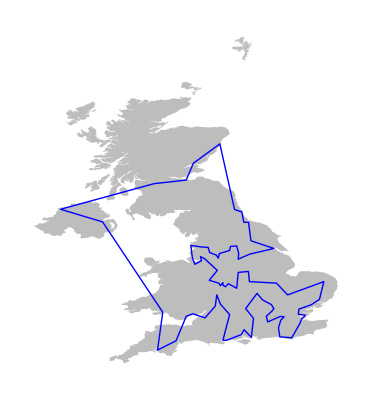

```mathematica
Graphics[{GrayLevel[0.74],CountryData["UnitedKingdom","Polygon"],Thick,Blue,Line[#[[Last[FindShortestTour[#]]]]&[Reverse[CityData[#,"Coordinates"]]&/@CityData[{Large,"UnitedKingdom"}]]]}]
```

## The Chinese Postman Problem

The Postman’s problem is subtly different from the Salesman’s. Where the salesman wanted to visit every city, or every edge of the graph, the postman wants to visit every vertex, in other words, every road. He doesn’t mind how many times he visits each edge, he only cares that he visits each vertex at least once. Imagining that we are a postman, we want to deliver mail to every house on every road on our map, so we have to walk down each road. Preferably, we don’t repeat roads, in order to minimize the effort and time it takes to deliver all our mail.

In Wolfram, we can use FindPostmanTour to give us the shortest route through all the vertices. Let’s look at a complete graph, a map where all the nodes are connected to each other. This graph is also directed, which means that we can only travel down the vertex in the direction of the arrow. We can animate the map to show the route we will take based on this algorithm.

This code takes a pre formatted graph and calculates an optimal tour using the FindPostmanTour algorithm built into Wolfram

```mathematica
g = -Graphics-; Shallow[tour=First[FindPostmanTour[g]]];
```

We then animate the path through the map, highlighting the node in yellow and the vertex in red as we travel along it.

```mathematica
color[tours_]:={tours,tours[[All,1]],Style[tours[[-1,2]],Yellow]};
Dynamic[HighlightGraph[g,color[tour[[1;;Clock[{1,Length[tour],1},40]]]]]]
```

## Further explorations

Eulerian cycles, a cycle that traverses every edge exactly once and returns to the starting edge. If your graph has a Eulerian cycle, then you can solve the Travelling Salesman Problem. If there are no Eulerian cycles, you can’t get an optimal solution (visiting each edge only once), but you can still visit each edge multiple times on your route, solving the Travelling Salesman Problem.

Hamiltonian cycles, a cycle that visits each vertex exactly once and returns to the start. Hamiltonian cycles can be useful in solving the Chinese Postman Problem.

Eulerian and Hamiltonian Paths do the same things, but do not return to the beginning.

## Author contact information

Rory Foulger

rfoulger@mac.com

https://roryfoulger.me/app